```mathematica
data=(Normal@RandomFunction[WienerProcess[0,.5],{0,1000,1}])[[1,;;,2]];
```

```mathematica
Autocorrelation=Total[(#1[[1+#2;;]]-Mean@#1)*(#1[[;;-1-#2]]-Mean@#1)]/Total[#1]^2&;
Autodifference=Total[((#1[[1+#2;;]]-Mean@#1)-(#1[[;;-1-#2]]-Mean@#1))^2]/Total[#1]^2&;
```

```mathematica
CorrelationFunction
```

CorrelationFunction

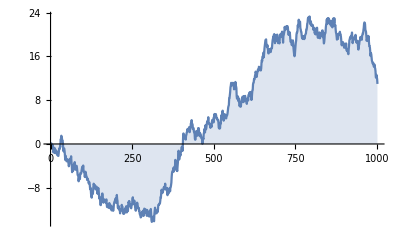

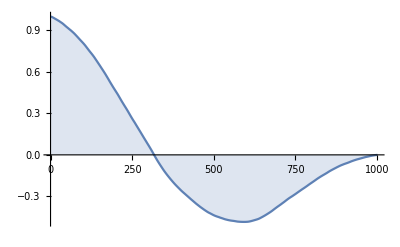

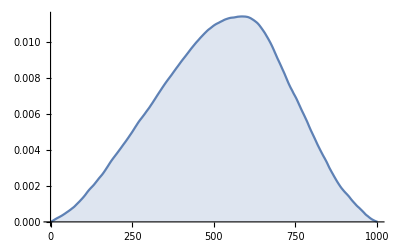

```mathematica
ListLinePlot[data,Filling->Axis]
ListLinePlot[Table[Autocorrelation[data,τ]/Autocorrelation[data,0],{τ,0,1000}],Filling->Axis]
ListLinePlot[Table[Autodifference[data,τ],{τ,0,1000}],Filling->Axis]
```

```mathematica
Autocorrelation[data,0]
```

0.

```mathematica
Autodifference[data,2]
```

0.000020497